# Prediction Opportunity MJO

BX Pan
2017.10.26

## Prediction Opportunity

On the Long Term Prediction of Chaotic System

Climate system undergoes different scenarios through its evolution. The slowly varying components can provide information for extended forecast. When dynamical models are initialized at certain phase of these  phenomena, the model forecasts match observations with more fidelity than the neutral phases. These intervals are named as forecast windows and believed to bring prediction opportunities.

## Examples

MJO

```mathematica
mjo=ImageCrop[-Graphics-];
ImageResize[mjo,1000]
```

-Graphics-

-Graphics- | -Graphics-"Meet the MJO, By Jon Gottschalck, NOAA Climate Prediction Center with Andrea Ray, WWA

Methodology

Cluster prediction results according to climate conditions and compare with long-run/neutral conditions.

The method applied here is a little bit different from ENSO.

For ENSO, it is generally easier to quantify/parameterize (even though there are different ENSO types, see this.

For MJO, the quantification/parameterization remains a problem given its organization and seasonality(Weickmann and Berry 2009, Dias et al. 2013, Waliser et al. 2012, Kikuchi et al. 2012, Lee et al.
2013, DeMott et al. 2013). 
The evolution of phase is important.

## MJO Indexes

Parameterization of MJO

1, filter OLR to retain only frequencies associated with the MJO. 
2, Filtered OLR between 208S and 208N is then subjected to a standard covariance matrix EOF analysis that retains the local variance of the OLR fluctuations.

```mathematica
MJO=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/ClimateIndex/MJO/OMI","Table"];
```

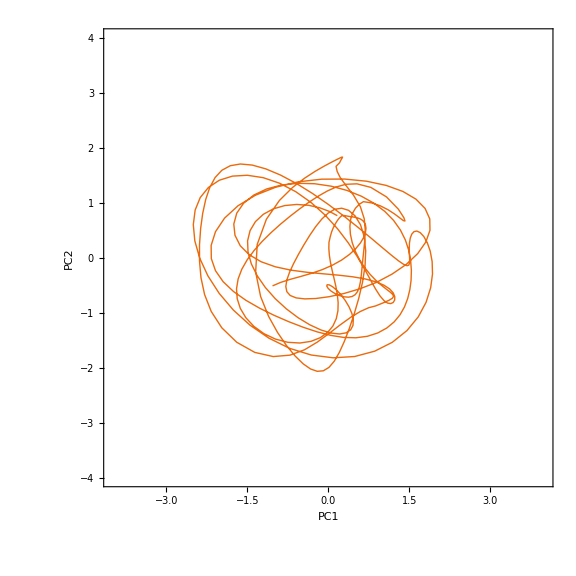

```mathematica
ListLinePlot[MJO[[1;;400,5;;6]],
	Frame->True,
	AspectRatio->1,
	ImageSize->Large,
	BaseStyle->25,
	FrameLabel->{"PC1","PC2"},
	PlotRange->{{-4,4},{-4,4}},
	GridLines->None,
	PlotStyle -> Directive[Thick, RGBColor[.8, 0, 0]], 
	ColorFunction -> (ColorData["SolarColors", #2] &)]
```

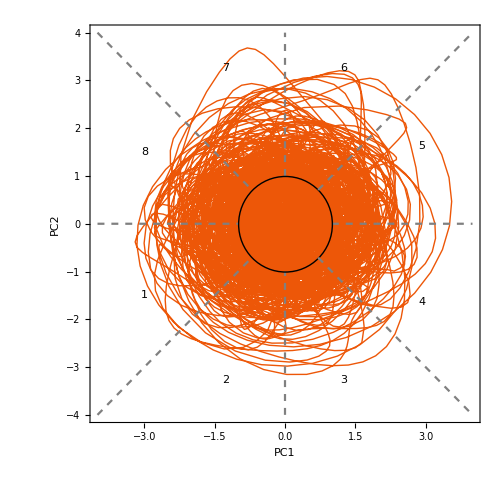

```mathematica
Show[
	{ListLinePlot[MJO[[;;,5;;6]],
	Frame->True,
	AspectRatio->1,
	ImageSize->Large,
	BaseStyle->25,
	FrameLabel->{"PC1","PC2"},
	PlotRange->{{-4,4},{-4,4}},
	GridLines->None,
	PlotStyle -> Directive[Thick, RGBColor[.8, 0, 0]], 
	ColorFunction -> (ColorData["SolarColors", #2] &)],
	Graphics[Circle[{0,0},1],AspectRatio->1],
	Plot[0,{x,-4,-1},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	Plot[0,{x,1,4},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	ListLinePlot[{{0,-4},{0,-1}},PlotStyle->{Gray,Dashed}],
	ListLinePlot[{{0,1},{0,4}},PlotStyle->{Gray,Dashed}],
	Plot[x,{x,-4,-Sqrt[2]/2},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	Plot[x,{x,Sqrt[2]/2,4},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	Plot[-x,{x,-4,-Sqrt[2]/2},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	Plot[-x,{x,Sqrt[2]/2,4},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	Graphics[Text["1", {-3, -1.5}, {0,0}]],
	Graphics[Text["2", {-1.26, -3.27}, {0,0}]],
	Graphics[Text["3", {1.26, -3.27}, {0,0}]],
	Graphics[Text["4", {2.92, -1.63}, {0,0}]],
	Graphics[Text["5", {2.92, 1.63}, {0,0}]],
	Graphics[Text["6", {1.26, 3.27}, {0,0}]],
	Graphics[Text["7", {-1.26, 3.27}, {0,0}]],
	Graphics[Text["8", {-3, 1.5}, {0,0}]]
	},
	AspectRatio->1,
	BaseStyle->25,
	Frame->True,
	ImageSize->500,
	FrameLabel->{"PC1","PC2"}]
```